## DATA ANALYSIS Axion off-diagonal couplings to quarks and leptons

#### Import Data

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

H:\2_Programming\physics\5d_flavourful_axion

```mathematica
<<"WarpFlavourAxion`"
```

```mathematica
(* Import and parse all round 3 data  *)
```

```mathematica
quarkData1 = {};
Do[ 
quarkData1 = quarkData1~Join~Import["data/quark"<>If[batch < 10,"0"<>ToString[batch], ToString[batch]]<>"round3.m"],
{batch, 9}
];
```

```mathematica
Length[quarkData1]
```

419

```mathematica
quarkData2={};
Do[
quarkData2=quarkData2~Join~Import["benchmark/3_"<>ToString[batch]<>".m"],
{batch,10}
];
```

```mathematica
Length[quarkData2]
```

442

```mathematica
quarkData = quarkData1~Join~quarkData2;
Length[quarkData]
```

861

```mathematica
leptonData = {
Import["data/leptonNH01round3.m"],
Import["data/leptonIH01round3.m"]
}
```

```mathematica
Length[leptonData[[1]]]
Length[leptonData[[2]]]
```

4323

3975

#### Find a set of c_P, c_M, convert to c_L, c_R

```mathematica
cMArray=Range[0.02,5.02,0.25]
With[{seed=0.001},
cuData={};
cdData={};
Do[
yu = quarkData[[i, 1]]; yd = quarkData[[i,2]];myu=Minors[quarkData[[i, 1]]];myd=Minors[quarkData[[i, 2]]];
AppendTo[cuData,
Table[
TurnLeft[({cM,cP}/.FindRoot[FermionProfileBulkOverlapCM[cP,cM]==QuarkEffMass[yu,yd,myu,myd][#],{cP,cM+seed}]&)/@{"u","c","t"}],
{cM,cMArray}
]//Quiet
];
AppendTo[cdData,
Table[
TurnLeft[({cM,cP}/.FindRoot[FermionProfileBulkOverlapCM[cP,cM]==QuarkEffMass[yu,yd,myu,myd][#],{cP,cM+seed}]&)/@{"d","s","b"}],
{cM,cMArray}
]//Quiet
];
,{i,Length[quarkData]}
]];//AbsoluteTiming
Clear[yu,yd,myu,myd]
Dimensions[cuData]
Dimensions[cdData]
```

#### Find the axion - fermions off-diagonal couplings

```mathematica
FermionAxionOverlap[c_,Δ_,zir_:10^8]:=(1-2c)/(zir^(1-2c) - 1)1/(4Δ(Δ-1)) ((zir^(1-2 c)-zir^(-2 Δ))/(1-2 c+2 Δ)+Δ(1/zir^2-zir^(1-2 c))/(3-2 c));
```

```mathematica
quarkAData = Table[
yu = quarkData[[i, 1]]; yd = quarkData[[i,2]];myu=Minors[quarkData[[i, 1]]];myd=Minors[quarkData[[i, 2]]];
QuarkAMatrices[yu, yd, myu, myd]
,{i,Length[quarkData]}
];//AbsoluteTiming
Clear[yu,yd,myu,myd]
Dimensions[quarkAData]
```

```mathematica
cuData//Dimensions
```

{861,21,3,2}

```mathematica
With[{Δ=9,k=1,cmpt=1, whichC = 2 (* cR *)},
quarkAData[[k,2]].
DiagonalMatrix[Table[FermionAxionOverlap[cuData[[k, cmpt, whichQuark, whichC]],Δ],{whichQuark,3}]].
ConjugateTranspose[ quarkAData[[k,2]] ]
]
```

{{-0.00781854-6.61744×10^-24 ⅈ,0.00001705+8.29778×10^-6 ⅈ,0.000021781+0.0000438708 ⅈ},{0.00001705-8.29778×10^-6 ⅈ,-0.00393245-1.00974×10^-28 ⅈ,0.0000922211-0.000645412 ⅈ},{0.000021781-0.0000438708 ⅈ,0.0000922211+0.000645412 ⅈ,-0.00010838+2.64696×10^-23 ⅈ}}

```mathematica
With[
{kMax = Dimensions[cuData][[1]], cmTotal =Dimensions[cuData][[2]], whichC = 2 (* cR *),Δ=9},
quarkNonuniversalCoupling9=Table[
quarkAData[[k,2]].
DiagonalMatrix[ Table[ FermionAxionOverlap[ cuData[[k, cmpt, whichQuark, whichC]] ,Δ],{whichQuark,3}] ].
ConjugateTranspose[ quarkAData[[k,2]] ],
{k,kMax},{cmpt,cmTotal}]
];
```

```mathematica
quarkNonuniversalCoupling9//Dimensions
```

{861,21,3,3}

Entry 12 of the axion coupling to the up quark

μ, σ of the log of the absolute values:

{-10.3947,1.02911}

Histogram of the absolute value and the phase

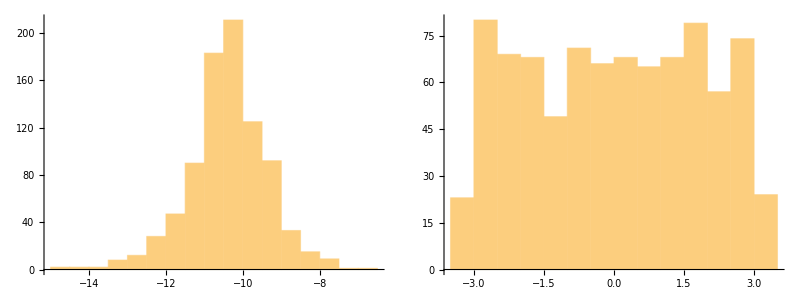

```mathematica
With[{cmpt=1, r = 1, c = 2},
sample = quarkNonuniversalCoupling9[[All,cmpt,r,c]];
Print["Entry ", r, c, " of the axion coupling to the up quark"];
Print["μ, σ of the log of the absolute values: "];
Print[Through[{Mean,StandardDeviation}[Log/@Abs[sample]]]];
Print["Histogram of the absolute value and the phase"];
Grid[{{Histogram[Log/@Abs[sample]],Histogram[Arg[sample]]}}]
]
```

Entry 13 of the axion coupling to the up quark

μ, σ of the log of the absolute values:

{-11.6382,1.1455}

Histogram of the absolute value and the phase

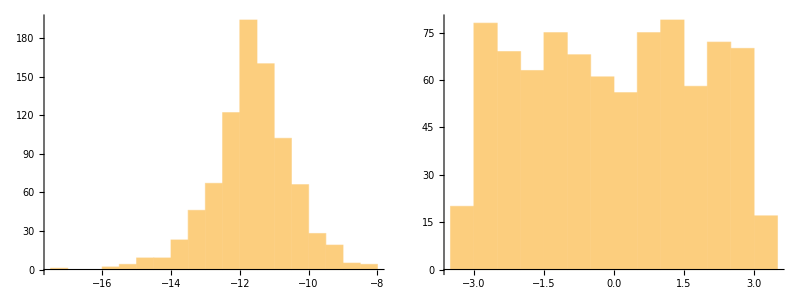

```mathematica
With[{cmpt=1, r = 1, c = 3},
sample = quarkNonuniversalCoupling9[[All,cmpt,r,c]];
Print["Entry ", r, c, " of the axion coupling to the up quark"];
Print["μ, σ of the log of the absolute values: "];
Print[Through[{Mean,StandardDeviation}[Log/@Abs[sample]]]];
Print["Histogram of the absolute value and the phase"];
Grid[{{Histogram[Log/@Abs[sample]],Histogram[Arg[sample]]}}]
]
```

Entry 23 of the axion coupling to the up quark

μ, σ of the log of the absolute values:

{-8.31817,1.15936}

Histogram of the absolute value and the phase

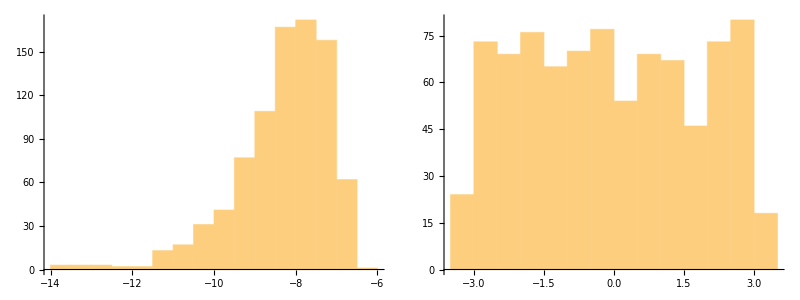

```mathematica
With[{cmpt=1, r = 2, c = 3},
sample = quarkNonuniversalCoupling9[[All,cmpt,r,c]];
Print["Entry ", r, c, " of the axion coupling to the up quark"];
Print["μ, σ of the log of the absolute values: "];
Print[Through[{Mean,StandardDeviation}[Log/@Abs[sample]]]];
Print["Histogram of the absolute value and the phase"];
Grid[{{Histogram[Log/@Abs[sample]],Histogram[Arg[sample]]}}]
]
```